```mathematica
r:=1100
```

```mathematica
c:=0.089 10^-6
```

```mathematica
rc:= r c
```

```mathematica
rc
```

0.0000979

```mathematica
Needs["ErrorBarPlots`"]
```

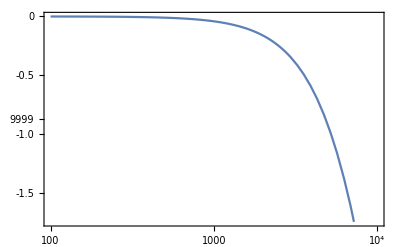

```mathematica
BodePlot[TransferFunctionModel[{1/(1+rc s)},s],{100,10000}][[1]][[1]][[1]]
```

```mathematica
data1:={{2,0,0,0.172003435238351},{2.30102999566398,-0.113656946607265,0,0.174246357679627},{2.47712125471966,-0.113656946607265,0,0.174246357679627},{2.69897000433602,-0.454675751454146,0,0.181151292469452},{2.84509804001426,-0.639685720127164,0,0.185009968673018},{2.90308998699194,-0.819172153578128,0,0.18883112465683},{2.95424250943932,-1.0024459192625,0,0.192813458722469},{3,-1.19963689984674,0,0.197190980584232},{3.04139268515822,-1.391208104666,0,0.201537803317342},{3.07918124604762,-5.48176735409904,0,0.320548908683015},{3.11394335230684,-1.79818908811864,0,0.211089116254387},{3.14612803567824,-2.00358995145807,0,0.2160780492421},{3.17609125905568,-2.22518078634215,0,0.221590834884073},{3.20411998265592,-2.6742532183161,0,0.233192250899867},{3.23044892137827,-2.66244371325002,0,0.232879623274154},{3.25527250510331,-2.90173955384289,0,0.239295840592866},{3.27875360095283,-3.13534443803981,0,0.245727551395813},{3.30102999566398,-3.37540612265873,0,0.127174887368959},{3.47712125471966,-5.81460078048338,0,0.168010840528627},{3.60205999132796,-7.7867967382024,0,0.210322373703105},{3.69897000433602,-9.57723832591927,0,0.257760447041974},{3.77815125038364,-10.9336331990592,0,0.300579807302389},{3.84509804001426,-12.2522034732254,0,0.348877805624172},{3.90308998699194,-13.3109249769814,0,0.393093759929403},{3.95424250943932,-14.333975425929,0,0.441002814861484},{4,-15.289431061849,0,0.490858821550518},{4.17609125905568,-18.7108402154616,0,0.718251117812891},{4.69897000433602,-29.3704216591549,0,0.25178254616041},{5,-34.8945498979339,0,0.469621916990455},{5.69897000433602,-46.0205999132796,0,1.5836249209525},{6,-50.4575749056067,0,2.498774732166}}
```

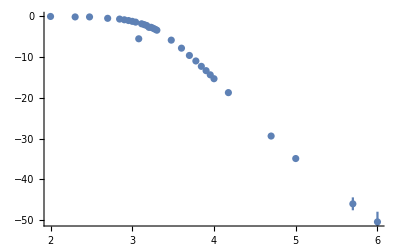

```mathematica
ErrorListPlot[{{#1,#2},ErrorBarPlots`ErrorBar@@{#3,#4}}&@@@data1,PlotRangePadding->{Scaled[0.15],Automatic}]
```

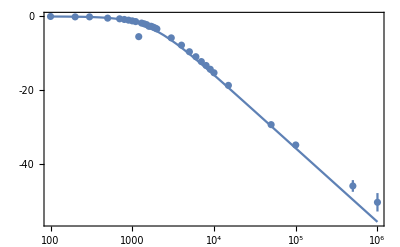

```mathematica
Show[BodePlot[TransferFunctionModel[{1/(1+ ts s)},s],{100,1000000}][[1]][[1]][[1]],ErrorListPlot[{{#1,#2},ErrorBarPlots`ErrorBar@@{#3,#4}}&@@@data1]]
```

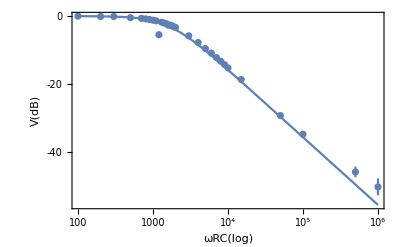

```mathematica
Show[%38,AxesLabel->{HoldForm[ωRC[log]],HoldForm[V[dB]]},PlotLabel->None,LabelStyle->{FontFamily->"Garamond Premier Pro",15,GrayLevel[0]}]
```

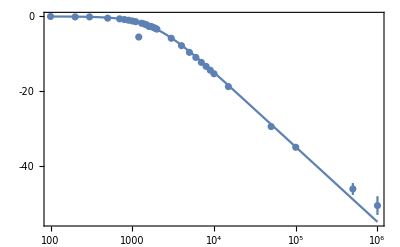

```mathematica
Show[%34,ImageSize->Full]
```

```mathematica
ts:=2 Pi rc
```

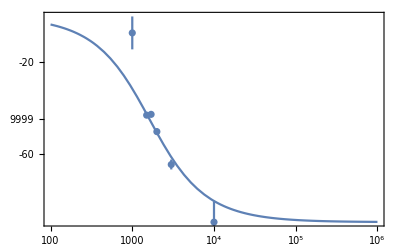

```mathematica
Show[BodePlot[TransferFunctionModel[{1/(1+ ts s)},s],{100,1000000}][[1]][[2]][[1]],ErrorListPlot[{{#1,#2},ErrorBarPlots`ErrorBar@@{#3,#4}}&@@@data2]]
```

```mathematica
Show[%47,PlotLabel->None,LabelStyle->{FontFamily->"Garamond Premier Pro",15,GrayLevel[0]}]
```

-Graphics-

```mathematica
data2:={{3,-7.2,0,7.2},{3.17609125905568,-43.2,0,1.08},{3.23044892137827,-42.84,0,1.224},{3.30102999566398,-50.4,0,1.44},{3.47712125471966,-64.8,0,2.16},{4,-90,0,9}}
```

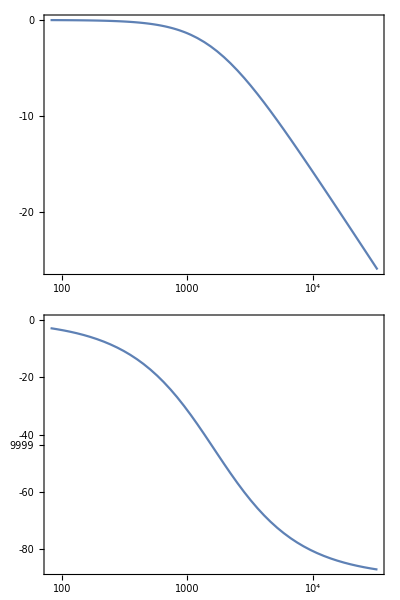

```mathematica
BodePlot[TransferFunctionModel[{1/(1+ ts s)},s]]
```

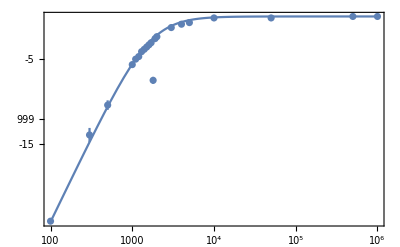

```mathematica
Show[BodePlot[TransferFunctionModel[{ts s/(1+ ts s)},s],{100,1000000}][[1]][[1]][[1]],ErrorListPlot[{{#1,#2},ErrorBarPlots`ErrorBar@@{#3,#4}}&@@@data3]]
```

```mathematica
Show[%51,PlotLabel->None,LabelStyle->{FontFamily->"Garamond Premier Pro",15,GrayLevel[0]}]
```

-Graphics-

```mathematica
data3:={{6,0,0,0.172003435238351},{5.69897000433602,0,0,0.172003435238351},{4.69897000433602,-0.175478486150103,0,0.175478486150103},{4,-0.175478486150103,0,0.175478486150103},{3.69897000433602,-0.724243453088894,0,0.186800525082868},{3.60205999132796,-0.915149811213502,0,0.190906358124608},{3.47712125471966,-1.31003097512865,0,0.199684418132018},{3.30102999566398,-2.38372815438417,0,0.225620208193781},{3.27875360095283,-2.61536560538048,0,0.231637450996303},{3.25527250510331,-7.53501419204199,0,0.40406772176574},{3.23044892137827,-3.09803919971486,0,0.244689128340231},{3.20411998265592,-3.34982174587527,0,0.251782546160411},{3.17609125905568,-3.60912128916263,0,0.259299543287353},{3.14612803567824,-3.87640052032226,0,0.26727923115963},{3.11394335230684,-4.15216621003492,0,0.275765689712667},{3.07918124604762,-4.73144012874126,0,0.294465136414127},{3.04139268515822,-5.03623945987599,0,0.304799331134736},{3,-5.67993312730402,0,0.327808323763388},{2.69897000433602,-10.4575749056068,0,0.560574472004872},{2.47712125471966,-13.9794000867204,0,0.8278537031645},{2,-24.1521662100349,0,0.138977199106556},{1.69897000433602,-28.8739499846543,0,0.237984465994153},{1,-36.4781748188864,0,1.5836249209525}}
```

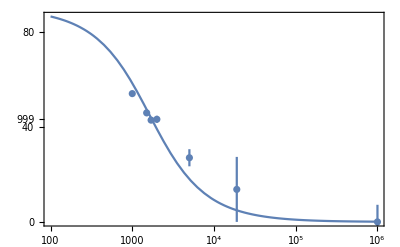

```mathematica
Show[BodePlot[TransferFunctionModel[{ts s/(1+ ts s)},s],{100,1000000}][[1]][[2]][[1]],ErrorListPlot[{{#1,#2},ErrorBarPlots`ErrorBar@@{#3,#4}}&@@@data4]]
```

```mathematica
Show[%54,PlotLabel->None,LabelStyle->{FontFamily->"Garamond Premier Pro",15,GrayLevel[0]}]
```

-Graphics-

```mathematica
data4:={{6,0,0,7.2},{4.27875360095283,13.68,0,13.68},{3.69897000433602,27,0,3.6},{3.30102999566398,43.2,0,1.44},{3.23044892137827,42.84,0,1.224},{3.17609125905568,45.9,0,1.35},{3,54,0,0.9}}
```

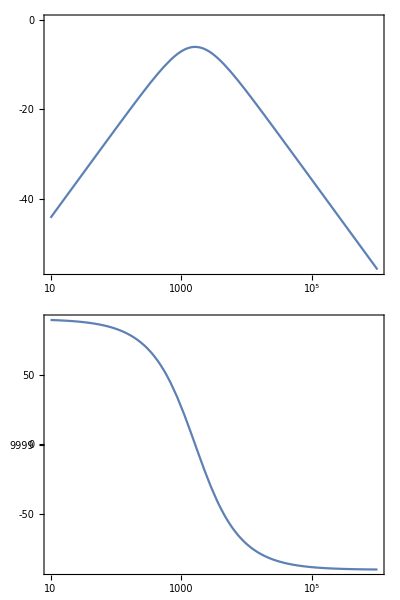

```mathematica
BodePlot[TransferFunctionModel[{ts s/(1+ ts s) (1/(1+ ts s))},s],{10,1000000}]
```

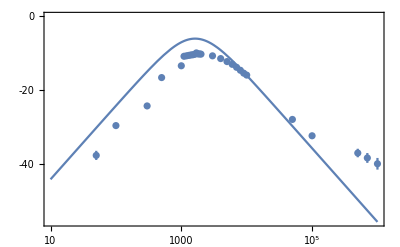

```mathematica
Show[BodePlot[TransferFunctionModel[{ts s/(1+ ts s) (1/(1+ ts s))},s],{10,1000000}][[1]][[1]][[1]],ErrorListPlot[{{#1,#2},ErrorBarPlots`ErrorBar@@{#3,#4}}&@@@data5]]
```

```mathematica
Show[%60,PlotLabel->None,LabelStyle->{FontFamily->"Garamond Premier Pro",15,GrayLevel[0]}]
```

-Graphics-

```mathematica
data5:={{1.69897000433602,-37.7211329538633,0,1.24295813497689},{2,-29.6297212024422,0,0.511082089447761},{2.47712125471966,-24.2934032997847,0,0.280214288856296},{2.69897000433602,-16.5947656921009,0,0.116590873214477},{3,-13.3917245330162,0,0.0807995560347994},{3.04139268515822,-10.8121502448154,0,0.0601102027945029},{3.07918124604763,-10.6923429710316,0,0.059289579274779},{3.11394335230684,-10.5741657788212,0,0.0584910603463324},{3.14612803567824,-10.4575749056068,0,0.0577137647497636},{3.17609125905568,-10.399861140857,0,0.0573328130320636},{3.20411998265593,-10.2855714703684,0,0.0565858003772846},{3.23044892137827,-9.89700043360188,0,0.0541178675184977},{3.25527250510331,-10.1727661233145,0,0.0558580036834027},{3.27875360095283,-10.1727661233145,0,0.0558580036834027},{3.30102999566398,-10.2289856699911,0,0.0562195466765676},{3.47712125471966,-10.6923429710316,0,0.059289579274779},{3.60205999132796,-11.4373041194242,0,0.0645794026039699},{3.69897000433602,-12.2522034732254,0,0.0709056152929932},{3.77815125038364,-12.9950396333167,0,0.0772084162647637},{3.84509804001426,-13.807396651482,0,0.0847410588650934},{3.90308998699194,-14.6097411156417,0,0.0928981009152707},{3.95424250943932,-15.3910215724345,0,0.101590510585497},{4,-15.9176003468815,0,0.107900637734122},{4.69897000433602,-27.9588001734407,0,0.423785981398762},{5,-32.3957751657679,0,0.69524212518424},{5.69897000433602,-37.0774392864352,0,1.15983893955374},{5.84509804001426,-38.4163750790475,0,1.33893579261226},{6,-40,0,1.5836249209525}}
```

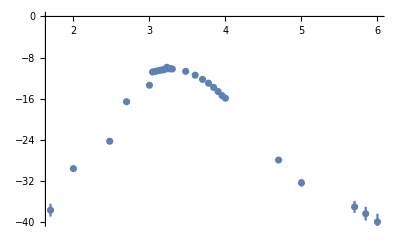

```mathematica
ErrorListPlot[{{#1,#2},ErrorBarPlots`ErrorBar@@{#3,#4}}&@@@data5]
```

```mathematica
Show[%61,PlotLabel->None,LabelStyle->{FontFamily->"Garamond Premier Pro",15,GrayLevel[0]}]
```

-Graphics-

```mathematica
vin:=1
```

```mathematica
r:=1100
```

```mathematica
c:= 0.089 10^-6
```

```mathematica
vc[f_]:=vin/Sqrt[1+(2 Pi f r c)^2]
```

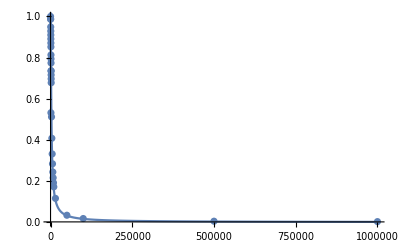

```mathematica
Show[Plot[vc[f],{f,0,1000000},PlotRange->Full],ErrorListPlot[{{#1,#2},ErrorBarPlots`ErrorBar@@{#3,#4}}&@@@dataa]]
```

```mathematica
dataa:={{100,1,0,0.02,0.001,100000},{200,0.987,0,0.02,0.000987,200000},{300,0.987,0,0.02,0.000987,300000},{500,0.949,0,0.02,0.000949,500000},{700,0.929,0,0.02,0.000929,700000},{800,0.91,0,0.02,0.00091,800000},{900,0.891,0,0.02,0.000891,900000},{1000,0.871,0,0.02,0.000871,1000000},{1100,0.852,0,0.02,0.000852,1100000},{1200,0.532,0,0.02,0.000532,1200000},{1300,0.813,0,0.02,0.000813,1300000},{1400,0.794,0,0.02,0.000794,1400000},{1500,0.774,0,0.02,0.000774,1500000},{1600,0.735,0,0.02,0.000735,1600000},{1700,0.736,0,0.02,0.000736,1700000},{1800,0.716,0,0.02,0.000716,1800000},{1900,0.697,0,0.02,0.000697,1900000},{2000,0.678,0,0.01,0.000678,2000000},{3000,0.512,0,0.01,0.000512,3000000},{4000,0.408,0,0.01,0.000408,4000000},{5000,0.332,0,0.01,0.000332,5000000},{6000,0.284,0,0.01,0.000284,6000000},{7000,0.244,0,0.01,0.000244,7000000},{8000,0.216,0,0.01,0.000216,8000000},{9000,0.192,0,0.01,0.000192,9000000},{10000,0.172,0,0.01,0.000172,10000000},{15000,0.116,0,0.01,0.000116,15000000},{50000,0.034,0,0.001,0.000034,50000000},{100000,0.018,0,0.001,0.000018,100000000},{500000,0.005,0,0.001,5.*^-6,500000000},{1000000,0.003,0,0.001,3.*^-6,1000000000}}
```

```mathematica
vr[f_]:=vin 2Pi f r c /Sqrt[1 + (2Pi f r c)^2]
```

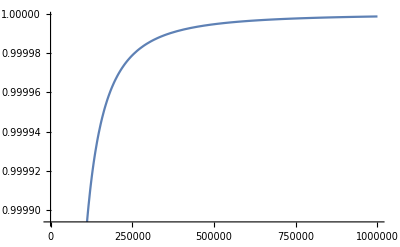

```mathematica
Plot[vr[f],{f,0,1000000}]
```

```mathematica
datab:={{1000,1000,1000000,1,0,0.02},{500,1000,500000,1,0,0.02},{50,980,50000,0.98,0,0.02},{10,980,10000,0.98,0,0.02},{5,920,5000,0.92,0,0.02},{4,900,4000,0.9,0,0.02},{3,860,3000,0.86,0,0.02},{2,760,2000,0.76,0,0.02},{1.9,740,1900,0.74,0,0.02},{1.8,420,1800,0.42,0,0.02},{1.7,700,1700,0.7,0,0.02},{1.6,680,1600,0.68,0,0.02},{1.5,660,1500,0.66,0,0.02},{1.4,640,1400,0.64,0,0.02},{1.3,620,1300,0.62,0,0.02},{1.2,580,1200,0.58,0,0.02},{1.1,560,1100,0.56,0,0.02},{1,520,1000,0.52,0,0.02},{0.5,300,500,0.3,0,0.02},{0.3,200,300,0.2,0,0.02},{0.1,62,100,0.062,0,0.001},{0.05,36,50,0.036,0,0.001},{0.01,15,10,0.015,0,0.003}}
```

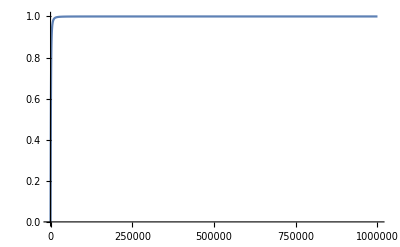

```mathematica
Show[Plot[vr[f],{f,0,1000000},PlotRange->Full],ErrorListPlot[{{#1,#2},ErrorBarPlots`ErrorBar@@{#3,#4}}&@@@datab]]
```